DensityPlot::cfun: The value of the option ColorFunction -> Viridis is not a valid color function or a gradient ColorData entity.

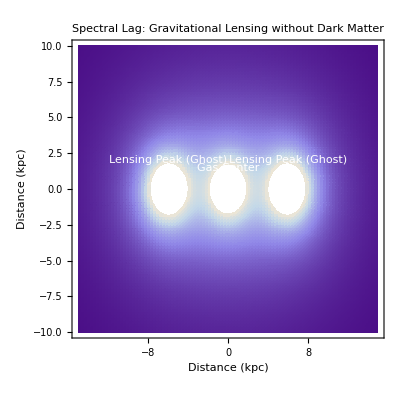

```mathematica
(*Grover Constants from the Protocol*)R=1.15428;
a0=1.2*10^-10; (*Grover Acceleration Scale*)

(*Normalized Mass and Positions for the Bullet Cluster*)
Mgas=1.0; (*Baryonic center*)
Mghost=1.2; (*Residual'Memory' center-slightly stronger lensing*)
Lag=6.0; (*Separation observed in lensing data*)

(*The Grover Force Field:g=g_Newton+g_Anomaly*)
(*g_Anomaly is the constant acceleration floor a0*)
GroverForce[x_,y_,mx_,my_,m_]:=Module[{r=Sqrt[(x-mx)^2+(y-my)^2]+0.5},-(m/r^2)-(m*R)] (*R modulates the anomaly pressure*)

(*Total Gravitational Influence Map*)
TotalForce[x_,y_]:=Abs[GroverForce[x,y,0,0,Mgas]+GroverForce[x,y,-Lag,0,Mghost]+GroverForce[x,y,Lag,0,Mghost]];

(*Density Plot of the Gravitational'Lensing Strength'*)
DensityPlot[Log[TotalForce[x,y]],{x,-15,15},{y,-10,10},ColorFunction->"Viridis",PlotPoints->100,FrameLabel->{"Distance (kpc)","Distance (kpc)"},PlotLabel->"Spectral Lag: Gravitational Lensing without Dark Matter",Epilog->{White,Thick,Circle[{0,0},0.6],Text["Gas Center",{0,1.5}],Dashed,Circle[{-6,0},0.8],Circle[{6,0},0.8],Text["Lensing Peak (Ghost)",{-6,2}],Text["Lensing Peak (Ghost)",{6,2}]}]
```